Run all tests

Starting test: Independent_Gamma_40_dim

Simulating using built-in method

Time to simulate: 0.375

Time to do CondMC + CondMO + AK: 322.531

Single Cond MC time: 5.35938

Cond MC time: 218.391

AK time: 320.859

Starting push-out estimator

Push-out took 12.7969

KDE beginning

It took: 0.546875

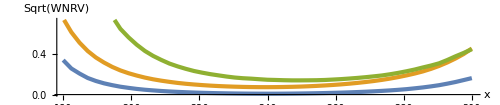
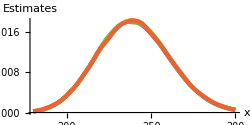
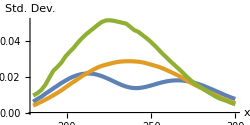

Independent_Gamma_40_dim done

Starting test: Clayton_Weibull_10_dim

Simulating using Marshall-Olkin form...

Time to simulate: 0.046875

Time to do CondMC + CondMO + AK: 591.828

Single Cond MC time: 59.2188

Cond MC time: 549.563

AK time: 588.875

Starting push-out estimator

Push-out took 182.063

KDE beginning

It took: 0.234375

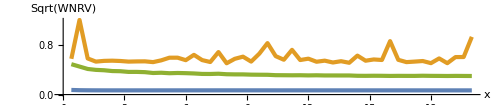
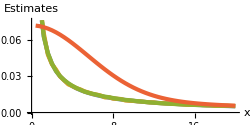
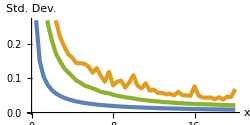

Clayton_Weibull_10_dim done

Starting test: GumbelHougaard_Exponential_15_dim

Simulating using Marshall-Olkin form...

Time to simulate: 0.046875

Time to do CondMC + CondMO + AK: 710.906

Single Cond MC time: 45.6875

Cond MC time: 645.875

AK time: 706.234

Starting push-out estimator

Push-out took 80.6563

KDE beginning

It took: 0.1875

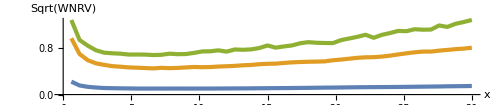
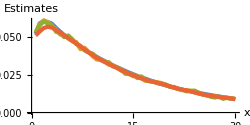
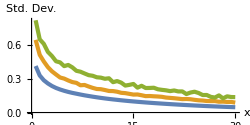

GumbelHougaard_Exponential_15_dim done

Starting test: Frank_LogNormal_10_dim

Simulating using built-in method

Time to simulate: 136.438

Time to do CondMC + CondMO + AK: 2473.44

Single Cond MC time: 382.313

Cond MC time: 2567.94

AK time: 2604.52

Starting push-out estimator

Push-out took 161.203

KDE beginning

It took: 151.766

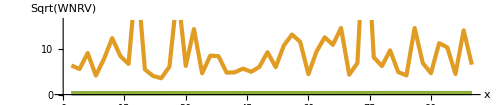
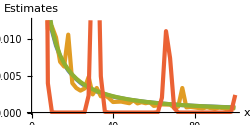
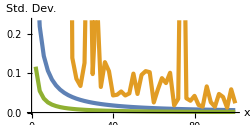

Frank_LogNormal_10_dim done

```mathematica
SetDirectory[NotebookDirectory[]];

GetCopulaInfo[Copula_]:=Module[{ϕ,ψ,ZDist,CopulaName,θ},
ZDist=None;
If[Copula=!="Product",
{CopulaName,θ}=Copula;
Switch[CopulaName,
"Clayton",
ϕ[u_]=(1+u/θ)^-θ;
ψ[u_]=θ (u^(-1/θ)-1);
ZDist=GammaDistribution[θ,1/θ];
,
"Frank",
ϕ[u_]=1/Log[θ] Log[1+Exp[-u] (Exp[Log[θ]]-1)];
ψ[u_]=-Log[ (Exp[Log[θ] u] - 1)/(Exp[Log[θ]]-1)],
"GumbelHougaard",
ϕ[u_]=Exp[-u^(1/θ)];
ψ[u_]=(-Log[u])^θ;
ZDist=StableDistribution[1,1/θ,1,0,Cos[Pi /(2θ)]^θ],
_,
ϕ=None;ψ=None
]];
{ϕ,ψ,ZDist}
];

Tests={
{"Product",GammaDistribution[3,2],40,{180,300}},
{{"Clayton",1/5},WeibullDistribution[3/10,1],10,{0,20}},
{{"GumbelHougaard",5},ExponentialDistribution[1],15,{0,30}},
{{"Frank", 1/1000},Table[LogNormalDistribution[i-10,√i],{i,10}],10,{0,100}}};

R=10^5;NumPoints=50;

Do[
SeedRandom[1];

(* Extract relevant copula properties for this test case *)
{Copula,Marg,n,sRange}=Test;

(* If given a list of marginals use them, otherwise take marginals to be identically distributed *)
Margs=If[ListQ[Marg], Marg, ConstantArray[Marg,n]];

(* Extract the simple form for the pdfs/cdfs assuming the input is inside the relevant support. *)
LBs=Table[Quantile[Margs[[i]],0],{i,n}];UBs=Table[Quantile[Margs[[i]],1],{i,n}];
PDFs=Table[Refine[PDF[Margs[[i]],Subscript[x, i]],Subscript[x, i]>LBs[[i]]&&Subscript[x, i]<UBs[[i]]],{i,n}];
CDFs=Table[Refine[CDF[Margs[[i]],Subscript[x, i]],Subscript[x, i]>LBs[[i]]&&Subscript[x, i]<UBs[[i]]],{i,n}];

XDist=CopulaDistribution[Copula,Margs];
{ϕ,ψ,ZDist}=GetCopulaInfo[Copula];

SingleCondIndex=n;

(* Create useful booleans for: i) is this the independent case, ii) does this copula have a Marshall-Olkin respresentation. *)
IsIndCopula=(Copula=== "Product");
HasMOForm=(ZDist=!=None);

ss= Range[sRange[[1]],sRange[[2]],(sRange[[2]]-sRange[[1]])/NumPoints]//DeleteCases[#,0]&;

TestName=If[IsIndCopula, "Independent",ToString[Copula[[1]]]]<>"_"<>StringTrim[ToString[Margs[[1,0]]],"Distribution"]<>"_"<>ToString[n]<>"_dim";
Print["Starting test: ", TestName];

(* Calculate the pdf of X using properties of Archimedean copulas *)
CPDF=If[IsIndCopula,1,
(D[ϕ[t],{t,n}]/.{t-> Sum[ψ[Subscript[u, i]],{i,n}]})*Product[ψ'[Subscript[u, i]],{i,n}]
];
IndPDF=Product[PDFs[[i]],{i,n}];
FullPDF=IndPDF*CPDF;

(* Sometimes the repeated CDF evaluation is very slow, so we do a trick to avoid repeated calls to this. *)
DelayMarginals=(Margs[[1,0]]===LogNormalDistribution);
If[!DelayMarginals,FullPDF=FullPDF/.Table[Subscript[u, i]->CDFs[[i]],{i,n}]];

(* If we have the Marshal-Olkin form, we simulate with this *)
If[HasMOForm,
Print["Simulating using Marshall-Olkin form..."];

Print["Time to simulate: ",SimulationTime= First@Timing[
Zs=RandomVariate[ZDist,R];
Vs=RandomVariate[ExponentialDistribution[1],{n,R}];

RVs=Transpose[Table[InverseCDF[Margs[[i]], ϕ[Vs[[i]]/Zs]],{i,n}]];
Sums=Total/@RVs;
]];
,
(* If not, just use Mathematica's builtin magic *)
Print["Simulating using built-in method"];
Print["Time to simulate: ", SimulationTime=First@Timing[
RVs=RandomVariate[XDist,R];
Sums=Total/@RVs;
]];
];

(* Calculate the CondMC and the AK estimates together. *)
Print["Time to do CondMC + CondMO + AK: ", First@Timing[
AllSingleConds=ConstantArray[0,{Length[ss],R}];
AllConds=ConstantArray[0,{Length[ss],R}];
AllAKs=ConstantArray[0,{Length[ss],R}];

SingleCondTime=SimulationTime;CondTime=SimulationTime;AKTime=SimulationTime;

(* Do each of the n versions of these estimators *)
Do[
If[R>10^5,Print["Starting CondMC+AK step ", LeaveOut," of ", n]];

(* Get the indices which are conditioned upon. *)
Others=DeleteCases[Range[n],LeaveOut];

(* Find the support of Margs[LeaveOut] *)
InSupport[x_]=If[UBs[[LeaveOut]]<∞,If[LBs[[LeaveOut]]>-∞,Boole[x>LBs[[LeaveOut]]&&x<UBs[[LeaveOut]]],Boole[x<UBs[[LeaveOut]]]],If[LBs[[LeaveOut]]>-∞,Boole[x>LBs[[LeaveOut]]],1 ]];

(* Find the conditional pdf of Subscript[X, LeaveOut] | Subscript[X, Others] *)
CondCPDF=If[IsIndCopula,1,
(D[ϕ[t],{t,n-1}]/.
{t-> Sum[ψ[Subscript[u, i]],{i,Others}]})*Product[ψ'[Subscript[u, i]],{i,Others}]
];
If[!DelayMarginals,CondCPDF=CondCPDF/.Table[Subscript[u, i]->CDFs[[i]],{i,n}]];

CondIndPDF=Product[PDFs[[i]],{i,Others}];
CondFullPDF=CondIndPDF*CondCPDF;

(* Calculate the maxima & sums of the Subscript[X, Others] vectors *)
{Mi,Si}=({Max[#],Total[#]}&/@RVs[[;;,Others]])ᵀ;

(* Calculate the standard CondMC estimates for each replicate & each s point. (CTime=  *)
CondTime+=(CTime=First@Timing[
(* If we have the Marshal-Olkin form, compute the extended CondMC estimator *)
If[HasMOForm,
fLeaveOut[x_]=PDFs[[LeaveOut]]/.{Subscript[x, LeaveOut]-> x};
FLeaveOut[x_]=CDFs[[LeaveOut]]/.{Subscript[x, LeaveOut]-> x};

Evals = Re@Table[
Pos=InSupport/@(s - Si);
Quiet[(-Zs* ψ'[FLeaveOut[s - Si]]Exp[-Zs   ψ[FLeaveOut[s - Si]]]fLeaveOut[s - Si] /.{Indeterminate-> 0,ComplexInfinity-> 0}) *Pos]
,{s,ss}];
AllConds += 1/n Evals;
,
(* Otherwise, use the slower/basic CondMC *)
Evals= Re@Table[
Pos=InSupport/@(s - Si);
CondToEval=FullPDF/CondFullPDF;

Repl=Flatten@{
Table[{
If[!FreeQ[CondToEval,Subscript[x, i]],Subscript[x, i]->RVs[[;;,i]],{}],
If[!FreeQ[CondToEval,Subscript[u, i]],Subscript[u, i]->CDF[Margs[[i]],RVs[[;;,i]]],{}]
},{i,Others}],
Subscript[x, LeaveOut]->s - Si,
If[!FreeQ[CondToEval,Subscript[u, LeaveOut]],Subscript[u, LeaveOut]-> CDF[Margs[[LeaveOut]],s - Si],{}]
};
Quiet[(CondToEval/.Repl/.{Indeterminate-> 0,ComplexInfinity-> 0})*Pos]
,{s,ss}];
AllConds+= 1/n Evals;
]
]);

(* If this is the special dimension for the 'single' CondMC estimator, store it separately. *)
If[LeaveOut==SingleCondIndex,
AllSingleConds = Evals;
SingleCondTime+=CTime;
];

(* Compute the Asmussen-Kroese density estimates by reusing the previously calculated conditional densities. *)
AKTime+=First@Timing[
AllAKs+=Table[Evals[[i]] Table[Boole[(Mi[[r]]< ss[[i]]-Si[[r]])],{r,R}],{i,Length[ss]}];
AKTime+=CTime;
];
, {LeaveOut,n}];

(* Calculate the final/combined estimates and their variances. *)
SingleCondTime+=First@Timing[{SingleConds,SingleCondVars}=({Mean[#],Variance[#]}&/@AllSingleConds)ᵀ];
CondTime+=First@Timing[{Conds,CondVars}=({Mean[#],Variance[#]}&/@AllConds)ᵀ];
AKTime+=First@Timing[{AKs,AKVars}=({Mean[#],Variance[#]}&/@AllAKs)ᵀ];
]
];

Print["Single Cond MC time: ",SingleCondTime];
Print["Cond MC time: ", CondTime];
Print["AK time: ",AKTime];

(* Perform the push-out estimator *)
Print["Starting push-out estimator"];
POPDF=FullPDF/.If[DelayMarginals,Table[Subscript[u, i]-> Subscript[u, i][Subscript[x, i]],{i,n}],
Table[Subscript[u, i]->CDFs[[i]],{i,n}]];

Print["Push-out took ",OurTime=SimulationTime+First@Timing[
(* Calculate the gradient of the log density at each replicate point.  *)
Derivs=Grad[Log[POPDF],Table[Subscript[x, i],{i,n}]];

Repl=Flatten@{
Table[{
If[!FreeQ[Derivs,Subscript[u, i]],{Subscript[u, i][Subscript[x, i]]->CDF[Margs[[i]],RVs[[;;,i]]],Subscript[u, i]'[Subscript[x, i]]->PDF[Margs[[i]],RVs[[;;,i]]]},{}],
If[!FreeQ[Derivs,Subscript[x, i]],Subscript[x, i]->RVs[[;;,i]],{}]
},{i,n}]
};

M=Transpose[Derivs/.Repl];
Grads=Table[RVs[[i]].M[[i]],{i,R}]+n;

(* Construct the two versions of the estimator, then make the approximately optimal mixture of them. *)
OurEsts=Table[
Inds= Table[Boole[Sr ≤ s],{Sr,Sums}];
Lefts= Grads *Inds/s;
Rights=- Grads * (1-Inds)/s;

PilotSize=Max[3,Ceiling[0.05*R]];
CC=Covariance[Transpose@{Lefts[[;;PilotSize]],Rights[[;;PilotSize]]}];
p=(CC[[2,2]]-CC[[1,2]])/(CC[[1,1]]+CC[[2,2]]-2CC[[1,2]]);

p*Lefts[[PilotSize+1;;]]+(1-p)Rights[[PilotSize+1;;]]
,{s,ss}];

{Ours,OurVars}=({Mean[#],Variance[#]}&/@OurEsts)ᵀ;
]];

Print["KDE beginning"];
Print["It took: ",KDETime=SimulationTime+ First@Timing[
KDEDist=KernelMixtureDistribution[Sums];
KDEs=PDF[KDEDist,ss]+PDF[KDEDist,-ss];]];

(* Setup for plotting *)
WithS[Data_]:=Transpose[{ss,Data}];
Colours=Lookup["DefaultPlotStyle"]@Lookup[Method]@Charting`ResolvePlotTheme[Automatic,Plot];

(* Create the plot of the estimates and for the relative errors. *)
EstimatorNames={"Push-out",(*"Single CondMC",*)"CondMC", "AK","KDE"};

EstimatesPlotSmall=
ListPlot[{WithS[Ours],(*WithS[SingleConds],*)WithS[Conds],WithS[AKs],WithS[KDEs]},Joined->True,ImageSize-> {250,125},AspectRatio->1/2,PlotStyle->Thickness[0.012],AxesLabel-> {"x","Estimates"}];

StdDevsPlotSmall=
ListPlot[{WithS[Sqrt@OurVars],(*WithS[Sqrt@SingleCondVars],*)WithS[Sqrt@CondVars],WithS[Sqrt@AKVars]},Joined->True,PlotStyle->Thickness[0.012],AxesLabel-> {"x","Std. Dev."},ImageSize->{250,125},AspectRatio->1/2];

SqrtWNRVPlot=
ListPlot[{WithS[√(OurTime * (OurVars/R)/Ours^2)],(*WithS[√(SingleCondTime * (SingleCondVars/R)/SingleConds^2)],*)WithS[√(CondTime * (CondVars/R)/Conds^2)],WithS[√(AKTime * (AKVars/R)/AKs^2)]},Joined->True,ImageSize-> {500,125},AspectRatio->0.21,PlotStyle->Thickness[0.006],AxesLabel-> {"x","Sqrt(WNRV)"}];

CombinedPlot=Legended[Column[{SqrtWNRVPlot,
Row[{EstimatesPlotSmall,StdDevsPlotSmall}]},Center],LineLegend[Colours,EstimatorNames]];
Print[CombinedPlot];
Export[TestName<>".pdf",CombinedPlot];
Print[TestName," done"];
,{Test,Tests}]
```